```mathematica
Options[Maze]={ImageSize->Automatic};

Maze[h_,w_,OptionsPattern[]]:=Module[{a={},b=True,temp,f},Monitor[f[x_]:=Select[x+#&/@{{0,1},{0,-1},{1,0},{-1,0}},FreeQ[a,#]&&If[Length[a]>h+w&&b,0<#[[1]]<h+1&&0<#[[2]]<w+1,1<#[[1]]<h&&1<#[[2]]<w]&&Intersection[a,{#+{0,1},#+{0,-1},#+{1,0},#+{-1,0}}]=={x}&];
AppendTo[a,RandomChoice[Flatten[{Table[{{1,i},{h,i}},{i,2,w-1}],Table[{{j,1},{j,w}},{j,2,h-1}]},2]]];
AppendTo[a,Select[Last[a]+#&/@{{0,1},{0,-1},{1,0},{-1,0}},1<#[[1]]<h&&1<#[[2]]<w&][[1]]];
While[Last[a][[1]]≠1&&Last[a][[1]]≠h&&Last[a][[2]]≠1&&Last[a][[2]]≠w,If[f[Last[a]]≠{},AppendTo[a,RandomChoice[f[Last[a]]]],a=RotateRight[a]];];b=False;
While[Select[a,#[[1]]≠1&&#[[1]]≠h&&#[[2]]≠1&&#[[2]]≠w&&f[#]≠{}&]≠{},temp=RandomChoice[Select[a,#[[1]]≠1&&#[[1]]≠h&&#[[2]]≠1&&#[[2]]≠w&&f[#]≠{}&]];
a=Append[Select[a,#≠temp&],temp];
While[Last[a][[1]]≠1&&Last[a][[1]]≠h&&Last[a][[2]]≠1&&Last[a][[2]]≠w&&f[Last[a]]≠{},AppendTo[a,RandomChoice[f[Last[a]]]];]];
Image[SparseArray[a->1,{h,w}],ImageSize->OptionValue[ImageSize]],ProgressIndicator[GoldenRatio*Length[a]/(w*h)]]];
```

```mathematica
a=Maze[40,60,ImageSize->600]
```

-Graphics-

```mathematica
b=ImageResize[a,600]
```

-Graphics-

```mathematica
c=Binarize[b,0.8]
```

-Graphics-

```mathematica
d=Thinning[c,Padding->1]
```

-Graphics-

```mathematica
e=Pruning[d,Infinity,Padding->1]
```

-Graphics-

```mathematica
f=Image[ArrayFlatten[Map[ConstantArray[#,{10,10}]&,ImageData[a],{2}]]]
```

-Graphics-

```mathematica
ImageSubtract[f,e]
```

-Graphics-

```mathematica
ImageApply[1-#&,Thinning[ImageApply[1-#&,c]]]
```

-Graphics-

```mathematica
Options[Maze3D]={Background->None,ImageSize->Automatic,Lighting->Automatic,PlotLabel->None,SphericalRegion->False,ViewAngle->Automatic,ViewCenter->Automatic,ViewMatrix->Automatic,ViewPoint->{1.3,-2.4,2.},ViewRange->All,ViewVector->Automatic,ViewVertical->{0,0,1}};

Maze3D[h_,w_,WallColor_,GroundColor_,OptionsPattern[]]:=Module[{a={},b=True,temp,f},Monitor[f[x_]:=Select[x+#&/@{{0,1},{0,-1},{1,0},{-1,0}},FreeQ[a,#]&&If[Length[a]>h+w&&b,0<#[[1]]<h+1&&0<#[[2]]<w+1,1<#[[1]]<h&&1<#[[2]]<w]&&Intersection[a,{#+{0,1},#+{0,-1},#+{1,0},#+{-1,0}}]=={x}&];
AppendTo[a,RandomChoice[Flatten[{Table[{{1,i},{h,i}},{i,2,w-1}],Table[{{j,1},{j,w}},{j,2,h-1}]},2]]];
AppendTo[a,Select[Last[a]+#&/@{{0,1},{0,-1},{1,0},{-1,0}},1<#[[1]]<h&&1<#[[2]]<w&][[1]]];
While[Last[a][[1]]≠1&&Last[a][[1]]≠h&&Last[a][[2]]≠1&&Last[a][[2]]≠w,If[f[Last[a]]≠{},AppendTo[a,RandomChoice[f[Last[a]]]],a=RotateRight[a]];];b=False;
While[Select[a,#[[1]]≠1&&#[[1]]≠h&&#[[2]]≠1&&#[[2]]≠w&&f[#]≠{}&]≠{},temp=RandomChoice[Select[a,#[[1]]≠1&&#[[1]]≠h&&#[[2]]≠1&&#[[2]]≠w&&f[#]≠{}&]];
a=Append[Select[a,#≠temp&],temp];
While[Last[a][[1]]≠1&&Last[a][[1]]≠h&&Last[a][[2]]≠1&&Last[a][[2]]≠w&&f[Last[a]]≠{},AppendTo[a,RandomChoice[f[Last[a]]]];]];
Graphics3D[{WallColor,Cuboid[Append[#,0]]&/@Complement[Join@@Table[{i,j},{i,h},{j,w}],a],GroundColor,Polygon[{{1,1,0},{h+1,1,0},{h+1,w+1,0},{1,w+1,0}}]},Boxed->False,Background->OptionValue[Background],ImageSize->OptionValue[ImageSize],Lighting->OptionValue[Lighting],PlotLabel->OptionValue[PlotLabel],SphericalRegion->OptionValue[SphericalRegion],ViewAngle->OptionValue[ViewAngle],ViewCenter->OptionValue[ViewCenter],ViewMatrix->OptionValue[ViewMatrix],ViewPoint->OptionValue[ViewPoint],ViewRange->OptionValue[ViewRange],ViewVector->OptionValue[ViewVector],ViewVertical->OptionValue[ViewVertical]],ProgressIndicator[GoldenRatio*Length[a]/(w*h)]]];

Maze3D[h_,w_,OptionsPattern[]]:=Maze3D[h,w,Brown,LightBrown,Background->OptionValue[Background],ImageSize->OptionValue[ImageSize],Lighting->OptionValue[Lighting],PlotLabel->OptionValue[PlotLabel],SphericalRegion->OptionValue[SphericalRegion],ViewAngle->OptionValue[ViewAngle],ViewCenter->OptionValue[ViewCenter],ViewMatrix->OptionValue[ViewMatrix],ViewPoint->OptionValue[ViewPoint],ViewRange->OptionValue[ViewRange],ViewVector->OptionValue[ViewVector],ViewVertical->OptionValue[ViewVertical]];
```

```mathematica
Options[MazeGame]={ImageSize->Automatic};

MazeGame[h_,w_,OptionsPattern[]]:=Module[{a={},b=True,temp,f,m0,m1},Monitor[f[x_]:=Select[x+#&/@{{0,1},{0,-1},{1,0},{-1,0}},FreeQ[a,#]&&If[Length[a]>h+w&&b,0<#[[1]]<h+1&&0<#[[2]]<w+1,1<#[[1]]<h&&1<#[[2]]<w]&&Intersection[a,{#+{0,1},#+{0,-1},#+{1,0},#+{-1,0}}]=={x}&];
AppendTo[a,m0=RandomChoice[Flatten[{Table[{{1,i},{h,i}},{i,2,w-1}],Table[{{j,1},{j,w}},{j,2,h-1}]},2]]];
AppendTo[a,Select[Last[a]+#&/@{{0,1},{0,-1},{1,0},{-1,0}},1<#[[1]]<h&&1<#[[2]]<w&][[1]]];
While[Last[a][[1]]≠1&&Last[a][[1]]≠h&&Last[a][[2]]≠1&&Last[a][[2]]≠w,If[f[Last[a]]≠{},AppendTo[a,RandomChoice[f[Last[a]]]],a=RotateRight[a]];];m1=Last[a];b=False;
While[Select[a,#[[1]]≠1&&#[[1]]≠h&&#[[2]]≠1&&#[[2]]≠w&&f[#]≠{}&]≠{},temp=RandomChoice[Select[a,#[[1]]≠1&&#[[1]]≠h&&#[[2]]≠1&&#[[2]]≠w&&f[#]≠{}&]];
a=Append[Select[a,#≠temp&],temp];
While[Last[a][[1]]≠1&&Last[a][[1]]≠h&&Last[a][[2]]≠1&&Last[a][[2]]≠w&&f[Last[a]]≠{},AppendTo[a,RandomChoice[f[Last[a]]]];]];
DynamicModule[{mm=m0},EventHandler[Dynamic[Image[SparseArray[Prepend[a,mm]->Prepend[ConstantArray[1,Length@a],0.5],{h,w}],ImageSize->OptionValue[ImageSize]]],{"LeftArrowKeyDown":>If[MemberQ[a,mm+{0,-1}],mm+={0,-1};
If[mm==m1,Speak["Good!"]]],"RightArrowKeyDown":>If[MemberQ[a,mm+{0,1}],mm+={0,1};
If[mm==m1,Speak["Good!"]]],"UpArrowKeyDown":>If[MemberQ[a,mm+{-1,0}],mm+={-1,0};
If[mm==m1,Speak["Good!"]]],"DownArrowKeyDown":>If[MemberQ[a,mm+{1,0}],mm+={1,0};
If[mm==m1,Speak["Good!"]]]}]],ProgressIndicator[GoldenRatio*Length[a]/(w*h)]]];
```

```mathematica
Options[Maze1]={ImageSize->Automatic};

Maze1[w_,h_,OptionsPattern[]]:=Module[{a={},b=True,g=Flatten[{Table[Line[{{i,j},{i,j+1}}],{i,w+1},{j,h}],Table[Line[{{i,j},{i+1,j}}],{i,w},{j,h+1}]},2],t,temp,f},Monitor[f[x_]:=Select[x+#&/@{{0,1},{0,-1},{1,0},{-1,0}},FreeQ[a,#]&&If[Length[a]>2 (w+h)&&b,0≤#[[1]]≤w+1&&0≤#[[2]]≤h+1,1≤#[[1]]≤w&&1≤#[[2]]≤h]&];
AppendTo[a,RandomChoice[Flatten[{Table[{{1,i},{w,i}},{i,2,h-1}],Table[{{j,1},{j,h}},{j,2,w-1}]},2]]];
g=DeleteCases[g,Which[a[[1,1]]==w,Line[{Last[a]+{1,0},Last[a]+{1,1}}],a[[1,1]]==1,Line[{Last[a]+{0,0},Last[a]+{0,1}}],a[[1,2]]==h,Line[{Last[a]+{0,1},Last[a]+{1,1}}],a[[1,2]]==1,Line[{Last[a]+{0,0},Last[a]+{1,0}}]]];
While[b,If[f[Last[a]]≠{},t=RandomChoice[f[Last[a]]];
g=DeleteCases[g,Switch[t-Last[a],{1,0},Line[{Last[a]+{1,0},Last[a]+{1,1}}],{-1,0},Line[{Last[a]+{0,0},Last[a]+{0,1}}],{0,1},Line[{Last[a]+{0,1},Last[a]+{1,1}}],{0,-1},Line[{Last[a]+{0,0},Last[a]+{1,0}}]]];
If[t[[1]]≠0&&t[[1]]≠w+1&&t[[2]]≠0&&t[[2]]≠h+1,AppendTo[a,t],b=False],a=RotateRight[a]]];
While[Select[a,f[#]≠{}&]≠{},temp=RandomChoice[Select[a,f[#]≠{}&]];
a=Append[Select[a,#≠temp&],temp];
While[f[Last[a]]≠{},t=RandomChoice[f[Last[a]]];
g=DeleteCases[g,Switch[t-Last[a],{1,0},Line[{Last[a]+{1,0},Last[a]+{1,1}}],{-1,0},Line[{Last[a]+{0,0},Last[a]+{0,1}}],{0,1},Line[{Last[a]+{0,1},Last[a]+{1,1}}],{0,-1},Line[{Last[a]+{0,0},Last[a]+{1,0}}]]];
AppendTo[a,t]]];
Graphics[{Thick,g},ImageSize->OptionValue[ImageSize]],ProgressIndicator[Length[a]/(w*h)]]];
```

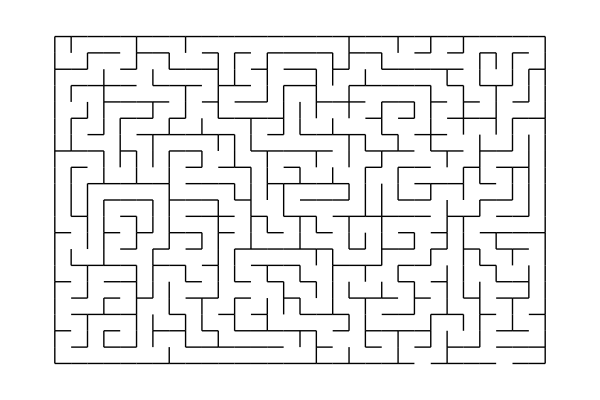

```mathematica
Maze1[30,20,ImageSize->600]
```